## “The mathematical facts worthy of being studied are those which...reveal the kinship between other facts, long known, but wrongly believed to be strangers to one another” ~ Henri Poincarè

# Orbigraphs are beautiful, discrete, analogues to Riemannian Orbifolds

Our definitions mirror Orbifolds

We can discern two classes of Orbigraphs

We mirror spectral results

# Discerning Classes of Orbigraphs

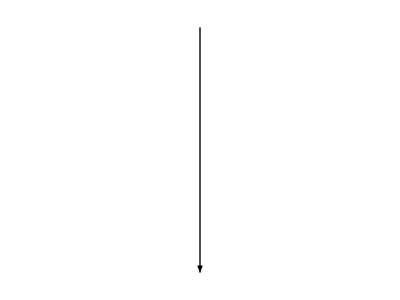
Orbifold Covering | 
-Graphics3D- | 
-Graphics- | 
Orbifold | 
-Graphics3D- |

```mathematica
AppendTo[$Path, NotebookDirectory[]];
<< "Orbigraphs.m";
<< "MarkovOrbigraphs.m";
<< "UniversalCoverings.m";
<< "OrbigraphCovers.m";

sphere = RevolutionPlot3D[{Sqrt[1-t^2],t},{t,-1,1},{θ,0,2π-Pi/3+Pi/30},PlotStyle->Blue,Mesh->12, Axes->False,Boxed->False];
partSphere = RevolutionPlot3D[{Sqrt[1-t^2],t},{t,-1,1},{θ,-Pi/3+Pi/30,0},Mesh->{12,1},PlotStyle->Red, Axes->False,Boxed->False];

goodOrbi = {{0,1,3},{1,0,3},{2,2,0}};
highlightColor =  RGBColor[255/255, 246/255,238/255];

cover = CreateFiniteCoveringGraph@goodOrbi;

goodOrbi = SetProperty[
AdjacencyOrbigraph@goodOrbi,
{
VertexSize->.1,
EdgeStyle->Directive[Thick, Black],
EdgeShapeFunction->GraphElementData["FilledArrow", "ArrowSize"-> .1],
EdgeLabelStyle->20,
VertexStyle->
{
1 -> RGBColor[204/255, 0,0],
2-> RGBColor[230/255, 193/255, 0],
3->RGBColor[180/255, 82/255, 204/255]
}
}

];

ShowCoveringGrid[slide_Integer] :=
Grid[
{
{
Style["Orbifold Covering", "Subsection",FontSize->Scaled[.030]],
If[slide > 1,Style["Orbigraph Covering", "Subsection",FontSize->Scaled[.030]], Spacer[1]]
},
{
Show[sphere,partSphere, ImageSize->Scaled[.4]],
If[slide > 1,SetProperty[cover,ImageSize->Scaled[.5]], Spacer[1]]
},

{
Item[
If[
slide > 0,
Graphics[{Arrowheads[.2],Arrow[{{0,.3},{0,-.3}}]}, ImageSize->Scaled[.3]],
Spacer[1]], 
Frame->{{False, False}, {True, True}}],
Item[
If[
slide > 1,
Graphics[{Arrowheads[.2],Arrow[{{0,.3},{0,-.3}}]}, ImageSize->Scaled[.3]],
Spacer[1]],
 Frame->{{False, False}, {True, True}},
 Background->White]
},
{
Style["Orbifold", "Subsection",FontSize->Scaled[.030]],
If[slide > 1,Style["Orbigraph", "Subsection",FontSize->Scaled[.030]], Spacer[1]]
},
{
If[
slide > 0,
RevolutionPlot3D[{.5*(1-x^2),x},{x,-1,1},{θ,0,2π},Mesh->{5,10},PlotStyle->Red,Axes->False,Boxed->False,ImageSize->Scaled[.3]],
Spacer[1]],
If[slide > 1, SetProperty[goodOrbi,ImageSize->Scaled[.5]], Spacer[1]]
}
},
Alignment->Center,
ItemSize->{{ Scaled[.5], Scaled[.5] }},
Background->{{White,highlightColor}},
Spacings->{Scaled[.02],Scaled[.02]},
Frame->All
]

ShowCoveringGrid[1]
```

```mathematica
ShowCoveringGrid[2]
```

Orbifold Covering | Orbigraph Covering
-Graphics3D- | -Graphics-
-Graphics- | -Graphics-
Orbifold | Orbigraph
-Graphics3D- | -Graphics-

```mathematica
teardrop=Piecewise[{{1/Sqrt[3]*x,x≤Sqrt[3]},{Sqrt[4/3-(x-4/Sqrt[3])^2],Sqrt[3]<x≤2*Sqrt[3]}}];
cone=RevolutionPlot3D[{teardrop,-x},{x,0,1},{θ,0,2π},Mesh->{5,10},PlotRange->{{-2,2},{-2,2},{-4,0}},PlotStyle->Red];
bulb=RevolutionPlot3D[{teardrop,-x},{x,1,2*Sqrt[3]},{θ,0,2π},Mesh->{10,10},PlotRange->{{-2,2},{-2,2},{-4,0}},Exclusions->None,PlotStyle->Blue];


footballF [x_]:=Piecewise[
{
{.9*(1-x^2),x > 0},
{.3*(3-x^2),x ≤ 0}
}] ;
footballBF [x_]:=Piecewise[
{
{.3*(1-x^2),x > 0},
{.1*(3-x^2),x ≤ 0}
}] ;

fatFootball = RevolutionPlot3D[{footballF[x],x},{x,-Sqrt[3], 1},{θ,0,2π-π/3},Mesh->{5,10},PlotStyle->Blue,Exclusions->None,Axes->False];

fatFootballSlice = Show[
RevolutionPlot3D[
{footballF[x],x},{x,-Sqrt[3],1},{θ,-π/3,0},
Mesh->{5,1},
PlotStyle->Red,
Axes->True,
Exclusions->None
]
];

slimFootball = Show[
RevolutionPlot3D[
{footballBF[x],x},{x,-Sqrt[3],1},{θ,0,2π},
Mesh->{5,1},
PlotStyle->Red,
Axes->True,
Exclusions->None
]
];

sphere = RevolutionPlot3D[{Sqrt[1-t^2],t},{t,-1,1},{θ,0,2π},PlotStyle->Blue, Axes->False];

(* four pillow code *)
vradius =.35;
hradius = .5;
f[x_, y_] := Piecewise[
{
{Sqrt[Abs[vradius^2(1 - (1/hradius^2 )y^2)]*(1 - 1/(hradius-y)^2 x^2)], 
y >= 0 && y < hradius},
{Sqrt[Abs[vradius^2(1 - (1/hradius^2 )y^2)]*(1 - 1/(hradius - -y)^2x^2)], 
y < 0 && y > -hradius},
{0, y < -hradius || y > hradius}
}
]

t = Plot3D[f[x,y], {x, -hradius,hradius},{y,-hradius,hradius}, AxesLabel->{x,y, z},Axes->False,Boxed->False,PlotStyle->Blue, Exclusions->None];
b =  Plot3D[-f[x,y], {x, -hradius,hradius},{y,-hradius,hradius}, AxesLabel->{x,y, z}, Axes->False,Boxed->False, PlotStyle->Blue,Exclusions->None];

planeBig = Plot3D[1 ,{x,-1,1}, {y,-1,1}, PlotStyle->Green, Mesh-> {4,4}, Axes->False, Boxed->False,RegionFunction->Function[{x,y,z}, -1/5≥  x ||x ≥  1/5 ||  -1/5 ≥ y|| y ≥ 1/5]];
planeSmall = Plot3D[ 1,{x, -1/5, 1/5}, {y, -1/5, 1/5} ,PlotStyle->Blue,Axes->False, Boxed->False,Mesh->0];

highlightColor =  RGBColor[255/255, 246/255,238/255];
ShowOrbifoldGrid[slide_Integer]:=Module[{},
Grid[
{
{
If[slide > 1, Style["Universal Cover", "Subsection", FontSize->Scaled[.020]], Spacer[1]],
Item[Spacer[1],Frame->{{True, True},{False, False}}],
If[slide> 0,Style["Orbifold", "Subsection", FontSize->Scaled[.020]],Spacer[1]],
Item[
Spacer[1],
Frame-> {{True, False}, {False, False}}
]
},
{
(* Plane*)
Item[
If[slide > 1, 
Show[planeBig, planeSmall, ImageSize->Scaled[1.0]], Spacer[1]]
],

(* Right arrow*)
Item[
If[slide > 1, 
Graphics[{Arrowheads[.3],Thickness[.05],Arrow[{{-.3,0},{.3,0}}]}, PlotRange->{{-.3, .3}, {-.1,.1}},ImageSize->Scaled[1.0]],Spacer[1]],
Frame->{{True, True},{False, False}}],

(* Four pillow*)
If[slide > 0, 
Overlay[{
Show[t, b, PlotRange->{{-hradius,hradius},{-hradius,hradius},{-hradius,hradius}},ImageSize->Scaled[1]],
Graphics[
If[slide > 2,
Translate[Rotate[Text[Style["Good", Bold, FontFamily->"Helvetica", FontSize->Scaled[.3], Darker@Green]], 40Degree], {1.0,0}],
{}
], 
ImageSize->Scaled[1.0]]
}],
Spacer[1]],
Item[
Spacer[1],
Frame-> {{True, False}, {False, False}}
]
},
{
(* fat football cover*)
If[slide > 1,
Show[fatFootball, fatFootballSlice,SphericalRegion->True,Axes->False,Boxed->False, ImageSize->Scaled[1]],
Spacer[1]],

(* right arrow*)
Item[
If[slide > 1,
Graphics[{Arrowheads[.3],Thickness[.05],Arrow[{{-.3,0},{.3,0}}]}, PlotRange->{{-.3, .3}, {-.1,.1}},ImageSize->Scaled[1.0]], Spacer[1]],
Frame->{{True, True},{False, False}}],

(* slim football*)
If[slide > 0,
Overlay[{
Show[slimFootball,SphericalRegion->True,Axes->False,Boxed->False,Background-> highlightColor, ImageSize->Scaled[1]] ,
Graphics[
If[slide > 3,
Translate[Rotate[Text[Style["Bad", Bold, FontFamily->"Helvetica", FontSize->Scaled[.3], Darker@Red]], 40Degree], {1.0,0}],
{}
], 
ImageSize->Scaled[1.0]]
}],
Spacer[1]
],
Item[
Spacer[1],
Frame-> {{True, False}, {False, False}}
]
}
},
Alignment->Center,
ItemSize->{{ Scaled[.25], Scaled[.10],Scaled[.25], Scaled[.35] }},
Spacings->{Scaled[.01],Scaled[.02]},
Background->{{White, White, highlightColor}},
Frame->All
]
];

ShowOrbifoldGrid[1]
```

|  | Orbifold | 
 |  | -Graphics3D--Graphics- | 
 |  | -Graphics3D--Graphics- |

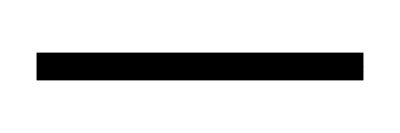
Universal Cover |  | Orbifold | 
-Graphics3D- | -Graphics- | -Graphics3D--Graphics- | 
-Graphics3D- | -Graphics- | -Graphics3D--Graphics- |

```mathematica
ShowOrbifoldGrid[2]
```

```mathematica
ShowOrbifoldGrid[3]
```

Universal Cover |  | Orbifold | 
-Graphics3D- | -Graphics- | -Graphics3D--Graphics- | 
-Graphics3D- | -Graphics- | -Graphics3D--Graphics- |

```mathematica
ShowOrbifoldGrid[4]
```

Universal Cover |  | Orbifold | 
-Graphics3D- | -Graphics- | -Graphics3D--Graphics- | 
-Graphics3D- | -Graphics- | -Graphics3D--Graphics- |

```mathematica
badOrbi = SetProperty[
AdjacencyOrbigraph[{{0,2,1},{1,0,2},{2,1,0}}],
{
VertexSize -> .09,
EdgeShapeFunction-> GraphElementData["FilledArrow", "ArrowSize"-> .1],
VertexStyle->
{
1 -> RGBColor[204/255, 0,0],
2-> RGBColor[230/255, 193/255, 0],
3->RGBColor[180/255, 82/255, 204/255]
},
EdgeLabelStyle -> 20,
ImageSize->Scaled[.4]
}
];

goodOrbi = SetProperty[
AdjacencyOrbigraph[{{0,1,3},{1,0,3},{2,2,0}}],
{
VertexSize -> .09,
VertexStyle->
{
1 -> RGBColor[204/255, 0,0],
2-> RGBColor[230/255, 193/255, 0],
3->RGBColor[180/255, 82/255, 204/255]
},
EdgeShapeFunction-> GraphElementData["FilledArrow", "ArrowSize"-> .1],
EdgeLabelStyle -> 20,
ImageSize->Scaled[.4]
}
];



ShowOrbigraphGrid[slide_Integer]:=
Grid[
{
{
If[slide > 1, Style["Infinite k-Tree Cover", "Subsection", FontSize-> Scaled[.02]], Spacer[1]],
Item[Spacer[1],
Frame->{{True, True}, {False, False}}
],
If[slide > 0, Style["Orbigraph", "Subsection", FontSize->Scaled[.02]], Spacer[1]],
Item[Spacer[1],
Frame->{{True, True}, {False, False}}
],
If[slide > 2, Style["Finite k-Regular Cover", "Subsection", FontSize->Scaled[.02]], Spacer[1]]
},
{
If[slide > 1, SetProperty[CreateUniversalCovering[goodOrbi,3], {VertexSize->.3,ImageSize->Scaled[1.0]}], Spacer[1]],
Item[
If[slide > 1, Graphics[{Arrowheads[.3],Thickness[.05],Arrow[{{-.3,0},{.3,0}}]}, PlotRange->{{-.3, .3}, {-.1,.1}},ImageSize->Scaled[1.0]], Spacer[1]],
Frame->{{True, True}, {False, False}}
],
If[slide > 0,

Overlay[
{
SetProperty[goodOrbi, ImageSize->Scaled[1.0]],

Graphics[
If[slide > 4,
Translate[Rotate[Text[Style["Good", Bold, FontFamily->"Helvetica", FontSize->Scaled[.3], Darker@Green]], 40Degree], {1.0,0}],
{}
], ImageSize->Scaled[1.0]]}],
Spacer[1]],
Item[
If[slide > 2,Graphics[{Arrowheads[.3],Thickness[.05],Arrow[{{.3,0},{-.3,0}}]}, PlotRange->{{-.3, .3}, {-.1,.1}},ImageSize->Scaled[1.0]], Spacer[1]],
Frame->{{True, True}, {False, False}}
],
If[slide > 2,
Item[
SetProperty[CreateFiniteCoveringGraph[Normal@WeightedAdjacencyMatrix@goodOrbi],{ImageSize->Scaled[1.0]}] ,
Background -> Opacity[.5, Green]
],
Spacer[1]
]
},
{
If[slide > 1,SetProperty[CreateUniversalCovering[badOrbi,4], {VertexSize->.3,
ImageSize->Scaled[1.0]}],Spacer[1]],
Item[
If[slide > 1,Graphics[{Arrowheads[.3],Thickness[.05],Arrow[{{-.3,0},{.3,0}}]}, PlotRange->{{-.3, .3}, {-.1,.1}},ImageSize->Scaled[1.0]],Spacer[1]],
Frame->{{True, True},{False, False}}
],
If[slide > 0,Overlay[{
SetProperty[badOrbi, ImageSize->Scaled[1.0]],
Graphics[
If[slide > 5,
Translate[Rotate[Text[Style["Bad", Bold, FontFamily->"Helvetica", FontSize->Scaled[.3], Red]], 40Degree], {1.0,0}],
{}
], ImageSize->Scaled[1.0]]}
],
Spacer[1]],
Item[
If[slide > 3,Graphics[{Arrowheads[.3],Thickness[.05],Arrow[{{.3,0},{-.3,0}}]}, PlotRange->{{-.3, .3}, {-.1,.1}},ImageSize->Scaled[1.0]],Spacer[1]],
Frame->{{True, True},{False, False}}
],
If[slide > 3,Item[
Text[Style["×", Red,FontSize->Scaled[.6], TextAlignment->Center]],
Background->Opacity[.3, Red]
],
Spacer[1]]
}
},

Alignment->Center,
ItemSize->{{Scaled[.25],Scaled[.10], Scaled[.25], Scaled[.10],  Scaled[.25]}},
Spacings->{Scaled[.01],Scaled[.02]},
Background->{{White, White,highlightColor, White}},
Frame->All
]


ShowOrbigraphGrid[1]
```

|  | Orbigraph |  | 
 |  | -Graphics--Graphics- |  | 
 |  | -Graphics--Graphics- |  |

```mathematica
ShowOrbigraphGrid[2]
```

Infinite k-Tree Cover |  | Orbigraph |  | 
-Graphics- | -Graphics- | -Graphics--Graphics- |  | 
-Graphics- | -Graphics- | -Graphics--Graphics- |  |

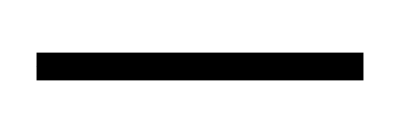
Infinite k-Tree Cover |  | Orbigraph |  | Finite k-Regular Cover
-Graphics- | -Graphics- | -Graphics--Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics--Graphics- |  |

```mathematica
ShowOrbigraphGrid[3]
```

```mathematica
ShowOrbigraphGrid[4]
```

Infinite k-Tree Cover |  | Orbigraph |  | Finite k-Regular Cover
-Graphics- | -Graphics- | -Graphics--Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics--Graphics- | -Graphics- | ×

```mathematica
ShowOrbigraphGrid[5]
```

Infinite k-Tree Cover |  | Orbigraph |  | Finite k-Regular Cover
-Graphics- | -Graphics- | -Graphics--Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics--Graphics- | -Graphics- | ×

```mathematica
ShowOrbigraphGrid[6]
```

Infinite k-Tree Cover |  | Orbigraph |  | Finite k-Regular Cover
-Graphics- | -Graphics- | -Graphics--Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics--Graphics- | -Graphics- | ×

```mathematica
badOrbi = SetProperty[
AdjacencyOrbigraph[{{0,3,1},{1,0,3},{3,1,0}}],
{
VertexSize -> .1,
EdgeStyle->Directive[Thick, Black],
EdgeLabelStyle->20,
EdgeShapeFunction->GraphElementData["FilledArrow", "ArrowSize"->.1],
VertexStyle->
{
1 -> RGBColor[204/255, 0,0],
2-> RGBColor[230/255, 193/255, 0],
3->RGBColor[180/255, 82/255, 204/255]
}
}
];

goodOrbi = SetProperty[
AdjacencyOrbigraph[{{0,1,3},{1,0,3},{2,2,0}}],
{
VertexSize->.1,
EdgeStyle->Directive[Thick, Black],
EdgeLabelStyle->20,
EdgeShapeFunction->GraphElementData["FilledArrow", "ArrowSize"->.1],
VertexStyle->
{
1 -> RGBColor[204/255, 0,0],
2-> RGBColor[230/255, 193/255, 0],
3->RGBColor[180/255, 82/255, 204/255]
}
}
];

dwnArrw = Graphics[{Arrowheads[.1],Arrow[{{0,.3},{0,-.3}}]}];

edgesToHighlight = {
{{}, Green},
{1->2, Green},
{2->3, Green},
{3->1,Green},
{1->3,Red},
{3->2,Red},
{2->1,Red},
{{}, Green}
};

textFrames = {
{"", "Subsection"},
{"3", "Subsection"},
{"3×3", "Subsection"},
{"3×3×3", "Subsection"},
{"3×3×3≠1", "Subsection"},
{"3×3×3≠1×1", "Subsection"},
{"3×3×3≠1×1×1", "Subsection"},
{"3×3×3≠1×1×1", "Subsection"},
};

edgesToHighlight2 = {
{{}, Green},
{{}, Green},
{1->2,Green},
{2->3,Green},
{3->1,Green},
{1->3,Red},
{3->2,Red},
{2->1,Red}
};

textFrames2= {
{"", "Subsection"},
{"", "Subsection"},
{"1", "Subsection"},
{"1×3", "Subsection"},
{"1×3×2", "Subsection"},
{"1×3×2=3", "Subsection"},
{"1×3×2=3×2", "Subsection"},
{"1×3×2=3×2×1", "Subsection"}
};



DisplayCycleGrid[slide_Integer]:=
Grid[
{
{
Item[
Style["Good Orbigraph", "Subsection",FontSize->Scaled[.02]],
Background->White],
Item[Spacer[1],Frame->{{True, True}, {False, False}}],
If[slide < 2, 
Style["Finite k-Regular Cover", "Subsection",FontSize->Scaled[.02]], 
Style["Finite k-Regular Cover?", "Subsection",FontSize->Scaled[.02]]
]
},
{

Column[{
Overlay[{
SetProperty[
HighlightGraph[goodOrbi,
Style[
First@edgesToHighlight2⟦#⟧,
Directive[Last@edgesToHighlight2⟦#⟧, Thick]
]&/@Range[Min[slide, 8]]
], ImageSize->Scaled[.5]
],
Graphics[
If[slide > 8,
(*Translate[Rotate[Text[Style["Bad", Bold, FontFamily->"Helvetica", FontSize->Scaled[.3], Red]], 40Degree], {1.0,0}],*)
Translate[Rotate[Text[Style["Good", Bold, FontFamily->"Helvetica", FontSize->Scaled[.5], Darker@Green]], 40Degree], {.5,0}],
{}
], ImageSize->Scaled[.5]]
}
],
Style[
First@textFrames2⟦Min[slide, 8]⟧,
Last@textFrames2⟦Min[slide, 8]⟧,
FontSize->Scaled[.020]
]
}
],
Item[
Graphics[{Arrowheads[.3],Thickness[.05],Arrow[{{.3,0},{-.3,0}}]}, PlotRange->{{-.3, .3}, {-.1,.1}},ImageSize->Scaled[1.0]],
Frame->{{True, True}, {False, False}}
],
Item[
If[slide < 2,
SetProperty[CreateFiniteCoveringGraph[Normal@WeightedAdjacencyMatrix@goodOrbi],{ImageSize->Scaled[.5]}] ,
Text[Style["?", Black,FontSize->Scaled[.5]]]
],
Background -> If[slide < 2, Opacity[.6, Green], White]
]
},
{
Item[
Style["Bad Orbigraph", 
"Subsection",
FontSize->Scaled[.02]
],
Background->White
],

Item[Spacer[1],Frame->{{True, True}, {False, False}}],

If[slide < 2,Style["No Finite k-Regular Cover", "Subsection",FontSize->Scaled[.02]], Style["No Finite k-Regular Cover?", "Subsection",FontSize->Scaled[.02]]
]
},
{
Column[{
Overlay[{
SetProperty[
HighlightGraph[badOrbi,
Style[
First@edgesToHighlight⟦#⟧,
Directive[Last@edgesToHighlight⟦#⟧, Thick]
]&/@Range[Max[slide -8, 1]]
],
ImageSize->Scaled[.5]
],
Graphics[
If[slide > 15,
Translate[Rotate[Text[Style["Bad", Bold, FontFamily->"Helvetica", FontSize->Scaled[.5], Red]], 40Degree], {.5,0}],
{}
], ImageSize->Scaled[.5]]
}
],
Style[
First@textFrames⟦Max[slide -8, 1]⟧,
Last@textFrames⟦Max[slide-8 , 1]⟧,
FontSize->Scaled[.02]
]
}
],
Item[
Graphics[{Arrowheads[.3],Thickness[.05],Arrow[{{.3,0},{-.3,0}}]}, PlotRange->{{-.3, .3}, {-.1,.1}},ImageSize->Scaled[1.0]],
Frame->{{True, True}, {False, False}}
],
Item[
If[slide < 2,
Text[Style["×", Red,FontSize->Scaled[.3], TextAlignment->Center]],
Text[Style["?", Black,FontSize->Scaled[.5]]]
],
Background->If[slide < 2, Opacity[.3, Red], White]
]
}
},
Alignment->Center,
ItemSize->{{ Scaled[.45],Scaled[.10],Scaled[.45 ]}},
Spacings->{Scaled[.03], Scaled[.009]},
Background->{{RGBColor[255/255, 246/255,238/255], White}},
Frame->All
];

DisplayCycleGrid[1]
```

Good Orbigraph |  | Finite k-Regular Cover
-Graphics--Graphics-
 | -Graphics- | -Graphics-
Bad Orbigraph |  | No Finite k-Regular Cover
-Graphics--Graphics-
 | -Graphics- | ×

```mathematica
DisplayCycleGrid[2]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
 | -Graphics- | ?

# Good/Bad Orbigraph Characterization (G., Stanhope, S., 2013)

```mathematica
DisplayCycleGrid[3]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
 | -Graphics- | ?

```mathematica
DisplayCycleGrid[4]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1×3 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
 | -Graphics- | ?

```mathematica
DisplayCycleGrid[5]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1×3×2 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
 | -Graphics- | ?

```mathematica
DisplayCycleGrid[6]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1×3×2=3 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
 | -Graphics- | ?

```mathematica
DisplayCycleGrid[7]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1×3×2=3×2 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
 | -Graphics- | ?

```mathematica
DisplayCycleGrid[8]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1×3×2=3×2×1 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
 | -Graphics- | ?

```mathematica
DisplayCycleGrid[9]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1×3×2=3×2×1 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
 | -Graphics- | ?

```mathematica
DisplayCycleGrid[10]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1×3×2=3×2×1 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
3 | -Graphics- | ?

```mathematica
DisplayCycleGrid[11]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1×3×2=3×2×1 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
3×3 | -Graphics- | ?

```mathematica
DisplayCycleGrid[12]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1×3×2=3×2×1 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
3×3×3 | -Graphics- | ?

```mathematica
DisplayCycleGrid[13]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1×3×2=3×2×1 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
3×3×3≠1 | -Graphics- | ?

```mathematica
DisplayCycleGrid[14]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1×3×2=3×2×1 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
3×3×3≠1×1 | -Graphics- | ?

```mathematica
DisplayCycleGrid[15]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1×3×2=3×2×1 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
3×3×3≠1×1×1 | -Graphics- | ?

```mathematica
DisplayCycleGrid[16]
```

Good Orbigraph |  | Finite k-Regular Cover?
-Graphics--Graphics-
1×3×2=3×2×1 | -Graphics- | ?
Bad Orbigraph |  | No Finite k-Regular Cover?
-Graphics--Graphics-
3×3×3≠1×1×1 | -Graphics- | ?

## Example: Randomly Generating Orbigraphs and Finite Covers

```mathematica
GenerateRandomReversibleOrbigraph[n_, k_] := Module[{randOrbi = GenerateRandomOrbigraph[n, k], tries=0},
While[tries ≤ 400 && Not[ConnectedOrbigraphQ[randOrbi]] || Not[OrbigraphReversibleQ[randOrbi]],
randOrbi = GenerateRandomOrbigraph[n, k];
tries++;
];
Return[randOrbi];
]

randOrbi = Graph[{1},{}, ImageSize-> 600];
coveringGraph = Graph[{1},{}];

Grid[
{
{
Item[
Dynamic[
If[VertexCount@randOrbi > 1, 
SetProperty[randOrbi,ImageSize->Scaled[1.0]],
Graphics[{}, ImageSize->Scaled[1.0]]
]
],
Frame->All],
 Graphics[{Arrowheads[.3],Thickness[.05],Arrow[{{-.3,0},{.3,0}}]}, PlotRange->{{-.3, .3}, {-.1,.1}},ImageSize->Scaled[1.0]],
Item[
Dynamic[
If[VertexCount@coveringGraph > 1, 
SetProperty[coveringGraph, ImageSize->Scaled[1.0]],
Graphics[{}, ImageSize->Scaled[1.0]]
]
],
Frame->All]
},
{
Button["Generate Random Orbigraph", 
Dynamic[
coveringGraph = Graph[{1},{}];
randOrbi = GenerateRandomReversibleOrbigraph[3,3];

randOrbi = SetProperty[
AdjacencyOrbigraph@randOrbi,
{
VertexSize->.3,
ImageSize->Scaled[1.0],
EdgeLabelStyle->15,
VertexStyle->
{
1 -> RGBColor[204/255, 0,0],
2-> RGBColor[230/255, 193/255, 0],
3->RGBColor[180/255, 82/255, 204/255]
}
}
]
],
ImageSize->Scaled[1.0]
],
Spacer[1],
Button["Generate Finite Covering",
Dynamic[coveringGraph = SetProperty[
CreateFiniteCoveringGraph[WeightedAdjacencyMatrix@randOrbi],
{ImageSize->Scaled[1.0], GraphLayout->"SpringEmbedding"}
];
],
ImageSize->Scaled[1.0]
]

}
},
Alignment-> Center,
ItemSize->{{Scaled[.43], Scaled[.10], Scaled[.43]}},
Spacings->{Scaled[.1], Scaled[.05]}
]
```

| -Graphics- | 
Generate Random Orbigraph |  | Generate Finite Covering

## Universal Covering Tree

```mathematica
sizes = SetProperty[CreateUniversalCovering[goodOrbi, #], VertexSize-> .2] &/@ Range[3];

GraphPlotRange[graph_Graph] := With[{embedding = GraphEmbedding@graph},
{{Min[First /@ embedding]-1, Max[First/@embedding]+1},{Min[Last/@embedding]-1, Max[Last/@embedding]+1}}]

Grid[{
{
SetProperty[goodOrbi,{EdgeLabelStyle->20,ImageSize->Scaled[.5]}],
ListAnimate[sizes, DefaultDuration->3, ImageSize->Scaled[1.0]]
}
},
Alignment-> {{Right, Left}},
ItemSize->{{ Scaled[.5], Scaled[.5]}},
Spacings->{Scaled[.1], 0}
]
```

-Graphics- |

## How did we discover and prove this connection?

Comes from Markov chain property “reversibility”

Reversible Markov chains satisfy the detailed balance equations: π_i P_(i, j)= π_j P_(j,i)

```mathematica
rightArrw = Graphics[{Arrowheads[.1],Arrow[{{-1.5,0},{1.5,0}}]}];
shortRightArrw = Graphics[{Arrowheads[.1],Arrow[{{0,0},{.3,0}}]}];

ro ={{0,2,1},{3,0,0},{2,0,1}};
P = ro/3;

markovChain = MarkovProcessFromOrbigraph@ro;

ro = SetProperty[
AdjacencyOrbigraph@ro,
{
ImageSize->Scaled[.3],
VertexSize->.1,
VertexStyle->
{
1-> Red, 
2-> Yellow,
3->Purple
}
}
];

totalCounts = 0;

GenerateRandomWalk[chain_DiscreteMarkovProcess, len_Integer] :=Module[{counts ,walk= {}, cur=1,next,i,  G = Graph@chain, T=Normal@MarkovProcessProperties[chain, "TransitionMatrix"]},
cur = RandomChoice[VertexList@G];
counts = {ConstantArray[0, VertexCount@G]};

 For[i = 0, i < len, i++, 
next = RandomChoice[Cases[T⟦cur⟧, x_/;x ≠ 0]-> Flatten[Position[T⟦cur⟧, x_/;x ≠ 0],1]];
walk = Append[walk, next];
counts = Append[counts, Last@counts];
counts⟦Length@counts,next⟧++; 
cur = next;
];

Return[{walk, counts}];
]


w = GenerateRandomWalk[markovChain, 5000];


Manipulate[
Grid[
{
{
HighlightGraph[
SetProperty[
ro, {
EdgeWeight-> N[PropertyValue[ro, EdgeWeight]/3],
EdgeLabelStyle-> 10,
EdgeStyle->Medium, 
VertexSize->.3,
ImageSize->Scaled[1.0]
}
]
, {Style[(First@w)⟦t⟧, Lighter@Pink]}],
Column[{
Style[StringJoin@{"π = [",Riffle[ToString@NumberForm[#,{2,2}]&/@N[(Last@w)⟦t⟧/t],", ", 2], "]"}, "Subsubsection",FontSize->Scaled[.02]],
Style[StringJoin@{"Steps: ",ToString@t}, "Subsubsection",FontSize->Scaled[.015]]
}
]
},
{
Grid[
{
{
Style["π_1P_(1, 2) = π_2P_(2, 1)", "Subsubsection",FontSize->Scaled[.02]],Style["π_1P_(1, 3) = π_3P_(3, 1)", "Subsubsection",FontSize->Scaled[.02]]
},
{
Style[StringJoin@{
ToString@NumberForm[If[t ≥ 4500, .31, P⟦1,2⟧ * N[(Last@w)⟦t⟧/t]⟦1⟧],{2,2}],
" = ", 
ToString@NumberForm[If[t ≥ 4500, .31, P⟦2,1⟧ * N[(Last@w)⟦t⟧/t]⟦2⟧],{2,2}]
},
"Subsubsection",FontSize->Scaled[.02]],
Style[StringJoin@{
ToString@NumberForm[If[t ≥ 4500, .16, P⟦1,3⟧ * N[(Last@w)⟦t⟧/t]⟦1⟧],{2,2}],
" = ", 
ToString@NumberForm[If[ t ≥ 4500, .16, P⟦3,1⟧ * N[(Last@w)⟦t⟧/t]⟦3⟧],{2,2}]
},
"Subsubsection",
FontSize->Scaled[.02]]
}
},
Frame->All,
Spacings->{3,1},
Alignment->Center
],
Style[MatrixForm[Normal[WeightedAdjacencyMatrix[ro]] / 3], "Subsubsection",FontSize->Scaled[.02]]
}

},
Alignment-> Center,
ItemSize->{{Scaled[.50], Scaled[.50]}}
],
{t, 1, Length@First@w, 1},
Alignment->Center
]
```

## Summary

The definition of Orbigraphs mirror Orbifolds

We can distinguish between good and bad orbigraphs

We can bound the number of singular points using the spectrum